```mathematica
imported =Import[FileNameJoin[{NotebookDirectory[],"output.json"}]];
T="time"/.imported;
V="volume"/.imported;ListPlot[Transpose[{T,V/V[[1]]}],Joined->True]
```

```mathematica
imported =Import[FileNameJoin[{NotebookDirectory[],"data.csv"}]];
imported[[1]]
imported=Take[imported,{2,Length[imported]}];

T=Transpose[imported][[1]];
H=Transpose[imported][[2]];
V=Transpose[imported][[3]];
```

{Time[s],Pressure[mbar],Position_smooth_splines [deg],Velocity[deg\s],Aceleration[deg\s2],Position_original [deg]}

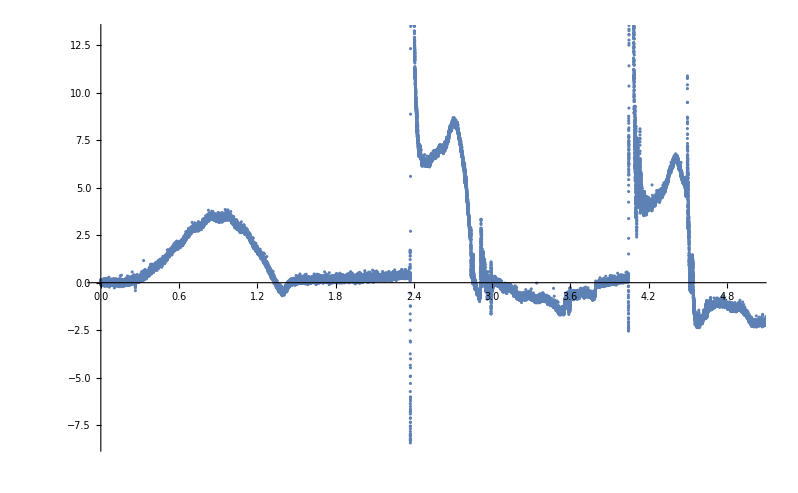

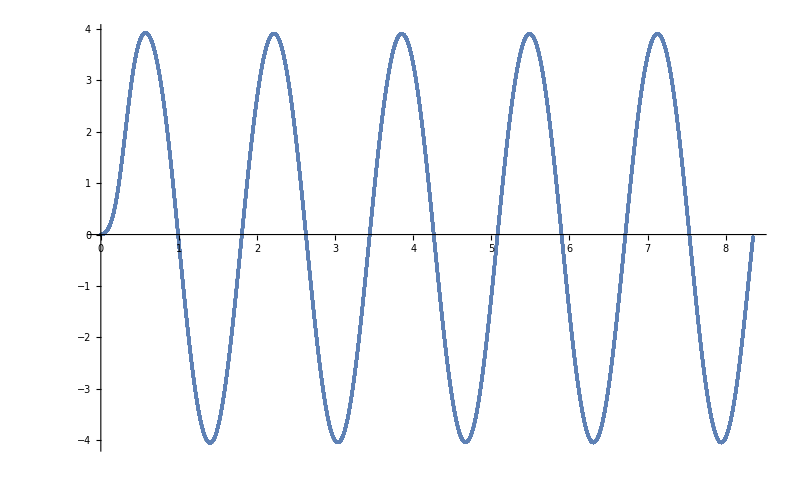

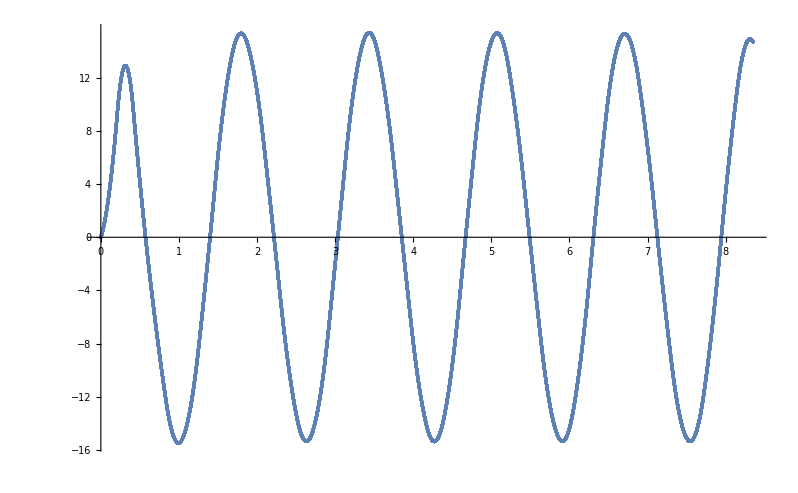

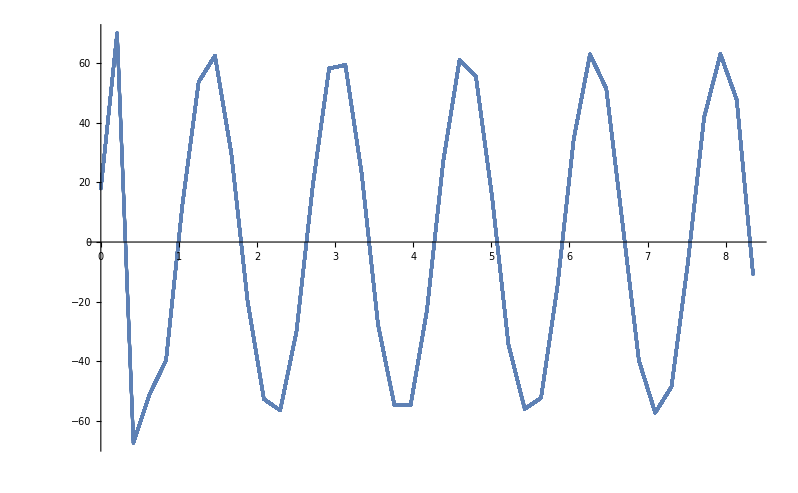

```mathematica
(*imported =Import["/Users/tomoaki/Downloads/SPHERIC_TestCase10/data_files/roof_water_1x.csv"];*)
imported =Import["/Users/tomoaki/Downloads/SPHERIC_TestCase10/data_files/lateral_water_1x.csv"];
imported[[1]]
imported=Take[imported,{2,Length[imported]}];

T=Transpose[imported][[1]];
X=Transpose[imported][[2]];
V=Transpose[imported][[3]];
A=Transpose[imported][[4]];
X0=Transpose[imported][[5]];
ListPlot[Transpose@{T,X},PlotRange->{{0,5},Automatic}]
ListPlot[Transpose@{T,V},PlotRange->All]
ListPlot[Transpose@{T,A},PlotRange->All]
ListPlot[Transpose@{T,X0},PlotRange->All]
```

```mathematica
(*{137,140,143,146,149,152,155,158,161,164,167,170,173,176,179,182,185,188,191,194,197,198,200,203,206,207,209,212,215,217,218,221,224,227,230,233,236,239,242,245,247,248,251,254,257,260,263,266,267,269,272,275,278,281,284,287}

{4.53,4.63,4.73,4.83,4.93,5.03,5.13,5.23,5.33,5.43,5.53,5.63,5.73,5.83,5.93,6.03,6.13,6.23,6.33,6.43,6.53,6.57,6.63,6.73,6.83,6.87,6.93,7.03,7.13,7.2,7.24,7.34,7.44,7.54,7.64,7.74,7.84,7.94,8.04,8.14,8.2,8.24,8.34,8.44,8.54,8.64,8.74,8.84,8.87,8.94,9.04,9.14,9.24,9.34,9.44,9.54}*)

H={10,9.9,9.8,10,11,11.2,10.4,9,8.5,9.2,12.2,13.4,11.4,8.3,7.5,8.2,12.2,16.2,13.8,8.6,6.6,6.6,7,11.2,18.2,19,18,10,6.2,5.8,6,8.2,17,21,16,7.2,5.6,6.4,12,20,22.8,22,11,7,5.8,7.6,16,24,24.8,23,10,7.2,7,11,20,22};

T={0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2,2.04,2.1,2.2,2.3,2.34,2.4,2.5,2.6,2.67,2.71,2.81,2.91,3.01,3.11,3.21,3.31,3.41,3.51,3.61,3.67,3.71,3.81,3.91,4.01,4.11,4.21,4.31,4.34,4.41,4.51,4.61,4.71,4.81,4.91,5.01};
```

{Time,max height (stats),max volume (stats)}

{Time,max height (stats),max volume (stats)}

{Time,max height (stats),max volume (stats)}

«1 more identical outputs»

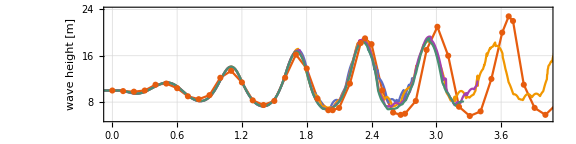

```mathematica
importedK001 =Import[FileNameJoin[{NotebookDirectory[],"heightK0.01.csv"}]];
importedK001[[1]]
importedK001=Take[importedK001,{2,Length[importedK001]}];

importedK05 =Import[FileNameJoin[{NotebookDirectory[],"heightK0.5.csv"}]];
importedK05[[1]]
importedK05=Take[importedK05,{2,Length[importedK05]}];

importedK01 =Import[FileNameJoin[{NotebookDirectory[],"heightK0.1.csv"}]];
importedK01[[1]]
importedK01=Take[importedK01,{2,Length[importedK01]}];

importedK10 =Import[FileNameJoin[{NotebookDirectory[],"heightK1.0.csv"}]];
importedK10[[1]]
importedK10=Take[importedK10,{2,Length[importedK10]}];

(*ListPlot[{#1,#2}&@@@imported,Joined->True,PlotTheme->"Scientific"]*)
ListPlot[{Transpose[{T,H}],
{#1-0.24,#2*100}&@@@importedK001,
{#1-0.24,#2*100}&@@@importedK01,
{#1-0.24,#2*100}&@@@importedK05,
{#1-0.24,#2*100}&@@@importedK10},
FrameStyle->Directive[Black, 12],
FrameLabel->{"time [s]","wave height [m]"},
Joined->{True,True,True,True,True},
PlotMarkers->{Automatic,False,False,False,False},
PlotLegends->{"Experiment",
"K=0.01",
"K=0.1",
"K=0.5",
"K=1.0"},
Joined->True,PlotTheme->"Scientific",PlotRange->{{0,4},{5,24}},GridLines->Automatic,ImageSize->Large,AspectRatio->1/4,ImageSize->1000]
```

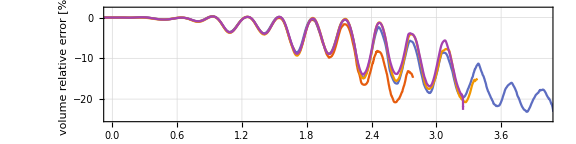

```mathematica
v001=(#3&@@@importedK001)[[1]];
v01=(#3&@@@importedK01)[[1]];
v05=(#3&@@@importedK05)[[1]];
v10=(#3&@@@importedK10)[[1]];
ListPlot[
{{#1-0.24,(#3-v001)/v001*100}&@@@importedK001,
{#1-0.24,(#3-v01)/v01*100}&@@@importedK01,
{#1-0.24,(#3-v05)/v05*100}&@@@importedK05,
{#1-0.24,(#3-v10)/v10*100}&@@@importedK10},
FrameStyle->Directive[Black, 12],
FrameLabel->{"time [s]","volume relative error [%]"},
PlotLegends->{
"K=0.01",
"K=0.1",
"K=0.5",
"K=1.0"},
Joined->True,PlotTheme->"Scientific",PlotRange->{{0,4},{2,-25}},GridLines->Automatic,ImageSize->Large,AspectRatio->1/4]
```

{Time,avg height (stats)}

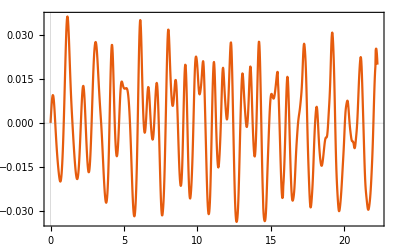

```mathematica
imported =Import["/Users/tomoaki/Dropbox/height.csv"];
imported[[1]]
imported=Take[imported,{2,Length[imported]}];

ListPlot[{#1,#2-0.18}&@@@imported,Joined->True,PlotTheme->"Scientific"]
```

```mathematica
4*π*1/20
```

π/5

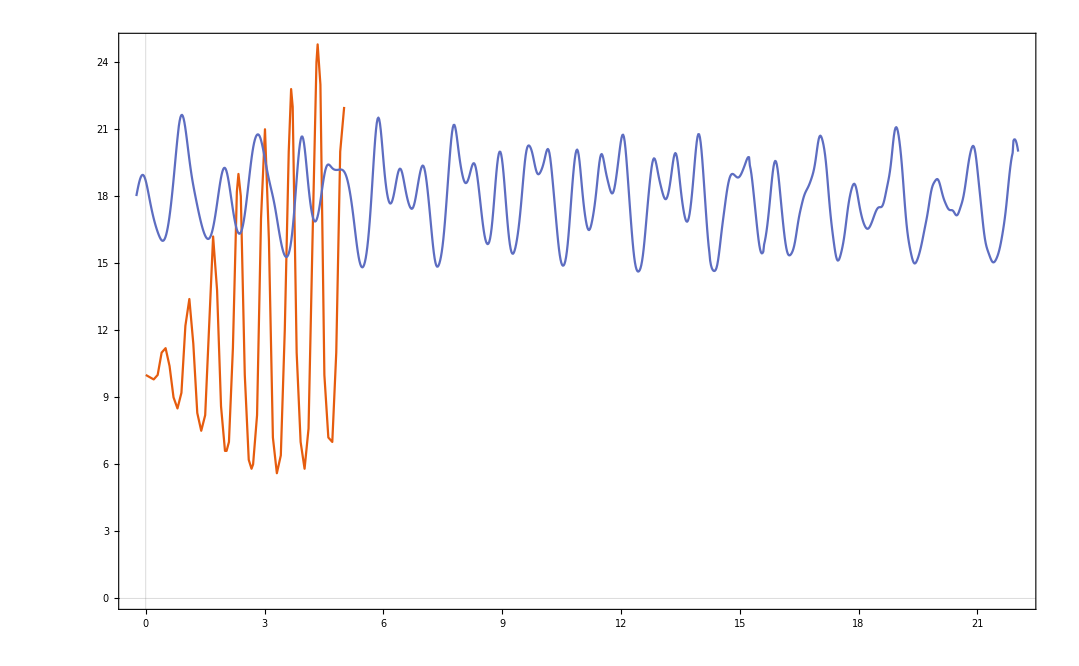

```mathematica
ListPlot[{Transpose[{T,H}],{#1-0.24,#2*100}&@@@imported},Joined->True,PlotTheme->"Scientific"]
```